## First implementation attempt of Infinite lists as functions

There are three types of infinite lists:
direction 1 lists  : open on the right side, closed on the left side. 	Example: {1,2,3,4,5,....}
direction -1 lists: open on the left side, closed on the right side. 	Example: {....,-5,-4,-3,-2,-1}
direction 0 lists  : open on both sides:						Example: {...,-3,-2,-1,0,1,2,---}

#### beginning of working definition : InfiniteList

```mathematica
InfiniteList[direction_,rule_][n_Integer]:= rule@n /;((direction==0)||(direction*n>0))
```

```mathematica
(*direction 0 lists HAVE AN "element 0". direction 1 lists only take positive numbers, direction -1 lists take only negative numbers*)
```

```mathematica
InfiniteList[direction_,rule_][n_Integer]:=Failure["InvalidInfinitePart",<|"MessageTemplate"->"Invalid infinite part specification"|>]/;Not@((direction==0)||(direction*n>0))
```

#### end of working definition

#### Scratch

```mathematica
InfiniteList[-1,#^3&][7]
```

Failure[…]

```mathematica
?AppendTo
```

AppendTo[s,elem] appends elem to the value of s, and resets s to the result.

```mathematica
?Append
```

Append[expr,elem] gives expr with elem appended. 
Append[elem] represents an operator form of Append that can be applied to an expression.

trying for direction 1 lists:

```mathematica
(* 
InfiniteListAppend[InfiniteList[direction_,rule_],elem_][1]:=elem;
InfiniteListAppend[InfiniteList[direction_,rule_],elem_][n_]:=rule@(n-1); 
WILL NOT WORK, NEEDS TO RETURN A InfiniteList*)
```

#### beginning of working definition: InfinitePrepend

```mathematica
(*Prepend only works for direction 1*)
InfinitePrepend[InfiniteList[direction_,rule_],elem_]:=
With[{newrule= If[#==1,elem,rule@(#-1)]&
}, InfiniteList[direction,newrule]]/;(direction==1 );

InfinitePrepend[InfiniteList[direction_,rule_],elem_]:=
Failure["InvalidInfinitePrepend",<|"MessageTemplate"->"InfinitePrepend only defined for right-open infinite lists"|>]/;(direction≠ 1 );
```

#### end of working definition

#### beginning of working definition: InfiniteAppend

```mathematica
(*Append only works for direction -1*)
InfiniteAppend[InfiniteList[direction_,rule_],elem_]:=
With[{newrule= If[#==-1,elem,rule@(#+1)]&
}, InfiniteList[direction,newrule]]/;(direction==-1 );

InfiniteAppend[InfiniteList[direction_,rule_],elem_]:=
Failure["InvalidInfinitePrepend",<|"MessageTemplate"->"InfinitePrepend only defined for left-open infinite lists"|>]/;(direction≠ -1 );
```

#### end of working definition

#### beginning of working definition: InfinitePart (one element)

```mathematica
InfinitePart[InfiniteList[direction_,rule_],n_Integer]:=rule@n /;((direction==0)||(direction*n>0));

InfinitePart[InfiniteList[direction_,rule_],n_Integer]:=Failure["InvalidInfinitePart",<|"MessageTemplate"->"Invalid infinite part specification"|>]/;Not@((direction==0)||(direction*n>0))
```

#### end of working definition

#### Scratch

```mathematica
InfiniteList[0,#&]
```

InfiniteList[0,#1&]

```mathematica
InfiniteAppend[InfiniteList[-1,#&],3][-5]
```

-4

```mathematica
InfinitePart[myLeftList,{-3,-4,-5}]
```

InfinitePart[myLeftList,{-3,-4,-5}]

```mathematica
InputForm[#^2 &]
```

#1^2 &

```mathematica
InputForm[x↦x^2]
```

Function[x, x^2]

```mathematica
myinfiniteList=InfiniteList[1,x↦Cos[x*π/10]]
```

InfiniteList[1,Function[x,Cos[(x π)/10]]]

```mathematica
myinfiniteList[1]
```

√(5/8+(√5)/8)

```mathematica
myAppendedList=InfiniteAppend[myinfiniteList,23]
```

Failure[…]

```mathematica
myAppendedList[1]
```

Failure[…][1]

```mathematica
myAppendedList[2]
```

Failure[…][2]

```mathematica
?Failure
```

Failure[tag,assoc] represents a failure of a type indicated by tag, with details given by the association assoc.

```mathematica
myInfiniteList=InfiniteList[1,Prime[#]&]
```

InfiniteList[1,Prime[#1]&]

```mathematica
myInfiniteList=InfiniteAppend[,343458345]
```

InfiniteAppend[Null,343458345]

#### Scratch

```mathematica
?IntegerDigits
```

IntegerDigits[n] gives a list of the decimal digits in the integer n. 
IntegerDigits[n,b] gives a list of the base b digits in the integer n. 
IntegerDigits[n,b,len] pads the list on the left with zeros to give a list of length len. 
IntegerDigits[n,MixedRadix[blist]] uses the mixed radix with list of bases blist.

```mathematica
?RealDigits
```

RealDigits[x] gives a list of the digits in the approximate real number x, together with the number of digits that are to the left of the decimal point. 
RealDigits[x,b] gives a list of base-b digits in x. 
RealDigits[x,b,len] gives a list of len digits. 
RealDigits[x,b,len,n] gives len digits starting with the coefficient of b^n.

```mathematica
myLeftList=InfiniteList[-1,Prime[-#]&];
myRightList=InfiniteList[1,Last@First[RealDigits[Pi,10,#]]&];
myZeroList=InfiniteList[0,#^3 &];
```

```mathematica
InfinitePart[myLeftList,-3]
```

5

```mathematica
InfinitePart[myRightList,6]
```

9

```mathematica
RealDigits[Pi,10,1]
```

{{3},1}

```mathematica
InfinitePart[myZeroList,-5]
```

-125

```mathematica
?Map
```

Map[f,expr] or f/@expr applies f to each element on the first level in expr. 
Map[f,expr,levelspec] applies f to parts of expr specified by levelspec. 
Map[f] represents an operator form of Map that can be applied to an expression.

```mathematica
?Range
```

Range[i_max] generates the list {1,2,…,i_max}. 
Range[i_min,i_max] generates the list {i_min,…,i_max}. 
Range[i_min,i_max,di] uses step di.

```mathematica
Range[-1,-4,-1]
```

{-1,-2,-3,-4}

#### beginning of working definition: InfinitePart(list of indexes)

```mathematica
(*only integers can be taken as indexs!*)
```

```mathematica
InfinitePart[InfiniteList[direction_,rule_],list_List/;AllTrue[list,IntegerQ]]:=InfinitePart[InfiniteList[direction,rule],list]=Map[rule,list]
```

```mathematica
InfinitePart[InfiniteList[direction_,rule_],list_List]:=Failure/;!AllTrue[list,IntegerQ]
```

```mathematica
(*this definitions needs to be refined! *)
```

#### End of working definition

#### Scratch

```mathematica
InfinitePart[myRightList,Range[10]]
```

{3,1,4,1,5,9,2,6,5,3}

```mathematica
Range[-1,-3,-1]
```

{-1,-2,-3}

```mathematica
InfinitePart[myZeroList,Range[-1,4]]
```

{-1,0,1,8,27,64}

```mathematica
InfinitePart[myRightList,{a,2}]
```

Failure

#### Beginning of working definition: InfiniteTake

```mathematica
(*based on InfinitePart*)
```

```mathematica
InfiniteTake[InfiniteList[direction_,rule_],n_Integer]:=InfinitePart[InfiniteList[direction,rule],Range[n]]/;(direction==1&&n>0);
```

```mathematica
InfiniteTake[InfiniteList[direction_,rule_],n_Integer]:=InfinitePart[InfiniteList[direction,rule],Range[-1,n,-1]]/;(direction==-1 &&n<0);
```

```mathematica
(* for direction -1 lists, InfiniteTake[#,n] returns in the order {-1,-2,-3,...,-Abs[n]}  *)
```

```mathematica
InfiniteTake[InfiniteList[direction_,rule_],n_Integer]:=Failure/;Not@Or[(direction==1&&n>0),(direction==-1 &&n<0)]
 (*This syntax covers all the cases!, beware, MUST be after all the other definitions*) (*Syntax was "/; True ", but it doesn't work when defining new cases :c, back to classic syntax*)
```

```mathematica
InfiniteTake[InfiniteList[direction_,rule_],{n_Integer,m_Integer}]:= InfinitePart[InfiniteList[direction,rule],Range[n,m,1]]/;
(direction==1&& n≤  m);
```

```mathematica
InfiniteTake[InfiniteList[direction_,rule_],{n_Integer,m_Integer}]:= InfinitePart[InfiniteList[direction,rule],Range[n,m,-1]]/;
(direction==-1&&m≤n<0);
 (*careful with the direction of the part in direction -1 lists!!*) 
(*InfiniteTake[mIL, {-4,-8}] = {mIL⟦-4⟧,mIL⟦-5⟧,...,mIL⟦-8⟧}  *) (*mIL is an arbitrary direction -1 infinite list*)
(*with this implementation we have:     InfiniteTake[mIL,{-1,-Abs[n]}]= InfiniteTake[mIL,-Abs[n]]  *)
```

```mathematica
InfiniteTake[InfiniteList[direction_,rule_],{n_Integer,m_Integer}]:= InfinitePart[InfiniteList[direction,rule],Range[n,m,1]]/;
(direction==0&&  n≤m );
```

```mathematica
InfiniteTake[InfiniteList[direction_,rule_],{n_Integer,m_Integer}]:=Failure/; Not@Or[(direction==1&& n≤  m),(direction==-1&&m≤n<0),(direction==0&&  n≤m )];
```

```mathematica
(*should infiniteTake also allow for expressions as {+2,Infinity}(direc 1 or 0) or {-Infinity,5} (direc -1 or 0) or {-Infinity,Infinity} (dir 0) ??????*)
```

```mathematica
(*beginning work of the 04.07 for this definition*)

InfiniteTake[InfiniteList[direction_,rule_],{n_Integer,Infinity}]:=
With[{newrule=rule@(#+n-1)&},InfiniteList[direction,newrule]]/;(direction==1&&n>0);
InfiniteTake[InfiniteList[direction_,rule_],{n_Integer,Infinity}]:=Failure/;Not@(direction==1&&n>0||direction==0);
```

```mathematica
InfiniteTake[InfiniteList[direction_,rule_],{-Infinity,n_Integer}]:=
With[{newrule=rule@(#+n+1)&},InfiniteList[direction,newrule]]/;(direction==-1&&n<0);
InfiniteTake[InfiniteList[direction_,rule_],{-Infinity,n_Integer}]:=Failure/;Not@(direction==-1&&n<0||direction==0);

InfiniteTake[InfiniteList[direction_,rule_],{-Infinity,Infinity}]:=InfiniteList[direction,rule]/;direction==0;
InfiniteTake[InfiniteList[direction_,rule_],{-Infinity,Infinity}]:=Failure/;Not@direction==0;
```

```mathematica
(*notice that direction 0 lists can get direction 1 or -1 lists taken from them!*)
InfiniteTake[InfiniteList[0,rule_],{n_Integer,Infinity}]:=
	With[{newrule=rule@(#+n-1)&},InfiniteList[1,newrule]];
```

```mathematica
InfiniteTake[InfiniteList[0,rule_],{-Infinity,n_Integer}]:=
	With[{newrule=rule@(#+n+1)&},InfiniteList[-1,newrule]];
```

```mathematica
(*end of work of the 04.07 for this definition*)
```

#### End of working definition

#### Scratch

```mathematica
myLeftList
```

InfiniteList[-1,Prime[-#1]&]

```mathematica
InfiniteTake[myLeftList,-5]
```

{2,3,5,7,11}

```mathematica
InfiniteTake[myLeftList,-5]
```

{2,3,5,7,11}

```mathematica
InfiniteTake[myLeftList,{-2,-5}]
```

{3,5,7,11}

```mathematica
Range[-4,-8]
```

{}

```mathematica
Range[-4,-8,-1]
```

{-4,-5,-6,-7,-8}

```mathematica
InfiniteTake[myZeroList,{-1,-3}]
```

Failure

```mathematica
Information[Failure]
```

Failure[tag,assoc] represents a failure of a type indicated by tag, with details given by the association assoc.

Attributes[Failure]={Protected,ReadProtected}

```mathematica
Length[{4,{},{}}]
```

3

```mathematica
InfiniteLength[myLeftList]
```

InfiniteLength[InfiniteList[-1,Prime[-#1]&]]

```mathematica
InfiniteTake[myRightList,{4,Infinity}]//InfinitePart[#,1]&
```

1

```mathematica
InfiniteTake[myZeroList,{-Infinity,Infinity}]//InfiniteTake[#,{-5,5}]&
```

{-125,-64,-27,-8,-1,0,1,8,27,64,125}

```mathematica
InfiniteTake[InfiniteList[0,#&],{-Infinity,Infinity}]
```

InfiniteList[0,#1&]

```mathematica
InfiniteTake[InfiniteList[0,#&],{-4,4}]
```

{-4,-3,-2,-1,0,1,2,3,4}

```mathematica
InfiniteTake[myZeroList,{-3,Infinity}]//InfiniteTake[#,5]&
```

{-27,-8,-1,0,1}

```mathematica
InfiniteTake[myZeroList,{-Infinity,2}]//InfiniteTake[#,-5]&
```

{8,1,0,-1,-8}

```mathematica
IntegerQ[Infinity]
```

False

```mathematica
Range[5,5]
```

{5}

#### Beginning of working definition: InfiniteLength

```mathematica
InfiniteLength[InfiniteList[direction_,rule_]]=Infinity; (*by far the easiest*)
```

#### End of working definition

#### Beginning of working definition: InfiniteDrop

```mathematica
InfiniteDrop[InfiniteList[direction_,rule_],n_Integer]:=
	With[{newrule= rule@(#+n)&},
	InfiniteList[direction,newrule]
]/;(direction==1 &&n>0);
```

```mathematica
InfiniteDrop[InfiniteList[direction_,rule_],n_Integer]:=
	With[{newrule= rule@(#+n)&}, (*"+n" even though n<0 *)
	InfiniteList[direction,newrule]
]/;(direction==-1 &&n<0);
```

```mathematica
InfiniteDrop[InfiniteList[direction_,rule_],n_Integer]:=Failure/; Not@Or[(direction==1 &&n>0),(direction==-1 &&n<0)]
```

```mathematica
InfiniteDrop[InfiniteList[direction_,rule_],{n_Integer}]:=
	With[{newrule=(If[#<n,rule@#, rule@(#+1)])&},
	InfiniteList[direction,newrule]]/;(direction==1&&n>0);
```

```mathematica
InfiniteDrop[InfiniteList[direction_,rule_],{n_Integer}]:=
	With[{newrule=(If[#>n,rule@#, rule@(#-1)])&},
	InfiniteList[direction,newrule]]/;(direction==-1&&n<0);
```

```mathematica
(*beginning work of the 05.07 on this definition*)
InfiniteDrop[InfiniteList[direction_,rule_],{n_Integer,m_Integer}]:=
	With[{newrule=If[#<n,rule@#,rule@(#+m-n+1)]&},
		InfiniteList[direction,newrule]]/;(direction==1&&0<n≤m);
InfiniteDrop[InfiniteList[direction_,rule_],{n_Integer,m_Integer}]:=
	With[{newrule=If[#>n,rule@#,rule@(#+m-n-1)]&},
InfiniteList[direction,newrule]]/;(direction==-1&&m≤n<0);

InfiniteDrop[InfiniteList[direction_,rule_],{n_Integer,m_Integer}]:=
(*problems if range includes index 0*)
Module[{newrule},
	newrule=Which[ n>0,If[#<n,rule@#,rule@(#+m-n+1)]&,
				   m<0,If[#>m,rule@#,rule@(#+n-m-1)]&,
				True,If[#≥0,rule@(#+m+1),rule@(#+n)]&] ;
(*remember n<0 in this case*)
InfiniteList[direction,newrule] ]/;(direction==0&&n≤m);

InfiniteDrop[InfiniteList[direction_,rule_],{n_Integer,m_Integer}]:=Failure/;Not@Or[(direction==1&&0<n≤m),(direction==-1&&m≤n<0),(direction==0&&n≤m)];
```

```mathematica
InfiniteDrop[InfiniteList[direction_,rule_],{n_Integer,Infinity}]:=
If[direction==1&&n==1,{},InfiniteTake[InfiniteList[direction,rule],n-1]]/;(direction==1&&n>0)
```

```mathematica
InfiniteDrop[InfiniteList[direction_,rule_],{n_Integer,Infinity}]:=
With[{newrule=rule@(#+n)&}, InfiniteList[-1,newrule]]/;direction==0
```

```mathematica
InfiniteDrop[InfiniteList[direction_,rule_],{n_Integer,Infinity}]:=Failure/;Not@Or[direction==0,(direction==1&&n>0)]
```

```mathematica
InfiniteDrop[InfiniteList[direction_,rule_],{-Infinity,n_Integer}]:=
If[direction==-1&&n==-1,{},Reverse@InfiniteTake[InfiniteList[direction,rule],n+1]]/;(direction==-1&&n<0) (*remember the Reverse!*)
```

```mathematica
InfiniteDrop[InfiniteList[direction_,rule_],{-Infinity,n_Integer}]:=
With[{newrule=rule@(#+n)&},InfiniteList[1,rule]]/;direction==0
```

```mathematica
InfiniteDrop[InfiniteList[direction_,rule_],{-Infinity,n_Integer}]:=Failure/;Not@Or[direction==0,(direction==-1&&n<0)]
```

```mathematica
InfiniteDrop[InfiniteList[direction_,rule_],{-Infinity,Infinity}]:={}/;direction==0
```

```mathematica
InfiniteDrop[InfiniteList[direction_,rule_],{-Infinity,Infinity}]:=Failure/;direction≠0
```

```mathematica
(*end of work of 05.07 on this definition*)
```

#### End of working definition

#### Scratch

```mathematica
InfiniteTake[myRightList,9]
```

{3,1,4,1,5,9,2,6,5}

```mathematica
InfiniteTake[InfiniteDrop[myRightList,4],5]
```

{5,9,2,6,5}

```mathematica
InfiniteTake[myLeftList,-10]
```

{2,3,5,7,11,13,17,19,23,29}

```mathematica
InfiniteTake[InfiniteDrop[myLeftList,-4],-6]
```

{11,13,17,19,23,29}

```mathematica
InfiniteTake[InfiniteDrop[myLeftList,-4],6]
```

Failure

```mathematica
InfiniteTake[InfiniteDrop[InfiniteList[1,#&],{4}],9]
```

{1,2,3,5,6,7,8,9,10}

```mathematica
InfiniteTake[InfiniteDrop[myRightList,{3}],9]
```

{3,1,1,5,9,2,6,5,3}

```mathematica
InfiniteTake[InfiniteDrop[myLeftList,{-3}],-9]
```

{2,3,7,11,13,17,19,23,29}

```mathematica
InfiniteTake[InfiniteDrop[myRightList,{2,4}],8]
```

{3,5,9,2,6,5,3,5}

```mathematica
InfiniteDrop[myRightList,{6,Infinity}]
```

{3,1,4,1,5}

```mathematica
InfiniteDrop[myRightList,{1,Infinity}]
```

{}

```mathematica
InputForm[myRightList⟦2;;6⟧]
```

Part::take: Cannot take positions 2 through 6 in InfiniteList[1,Last[First[RealDigits[π,10,#1]]]&].

InfiniteList[1, Last[First[RealDigits[Pi, 10, #1]]] & ][[2 ;; 6]]

```mathematica
InfiniteDrop[myLeftList,{-4,-6}]//InfiniteTake[#,-10]&
```

{2,3,5,17,19,23,29,31,37,41}

```mathematica
InfiniteDrop[myZeroList,{2,4}]//InfiniteTake[#,{-7,5}]&
```

{-343,-216,-125,-64,-27,-8,-1,0,1,125,216,343,512}

```mathematica
Pi
```

π

#### Scratch

```mathematica
InfiniteDrop[myZeroList,{3,Infinity}]//InfiniteTake[#,-8]&
```

{8,1,0,-1,-8,-27,-64,-125}

```mathematica
InfiniteDrop[myLeftList,{3,Infinity}]
```

Failure

```mathematica
InfiniteDrop[myLeftList,{-Infinity,-1}]
```

{}

```mathematica
InfiniteDrop[myRightList,{-Infinity,4}]
```

Failure

```mathematica
InfiniteDrop[myZeroList,{-Infinity,Infinity}]
```

{}

```mathematica
InfiniteDrop[myLeftList,{-Infinity,Infinity}]
```

Failure

```mathematica
Pi
```

π

#### Beginning of working definition: InfiniteFirst, InfiniteLast, Infinite Direction

```mathematica
(*First only makes sense for direction 1 lists*)
InfiniteFirst[InfiniteList[direction_,rule_]]:=rule@1/;direction==1
InfiniteFirst[InfiniteList[direction_,rule_]]:=Failure/;direction≠1

(*last only makes sense for direction -1 lists*)
InfiniteLast[InfiniteList[direction_,rule_]]:=rule@(-1)/;direction==-1
InfiniteLast[InfiniteList[direction_,rule_]]:=Failure/;direction≠ -1
```

```mathematica
(*InfiniteDirection returns the direction of the list*)
InfiniteDirection[InfiniteList[direction_,rule_]]:=direction;
```

#### End of working definition

#### Scratch

```mathematica
InfiniteFirst[myRightList]
```

3

```mathematica
InfiniteFirst[myLeftList]
```

Failure

```mathematica
InfiniteFirst[myZeroList]
```

Failure

```mathematica
InfiniteLast[myLeftList]
```

2

```mathematica
InfiniteLast[myRightList]
```

Failure

```mathematica
InfiniteDirection/@{myRightList,myZeroList,myLeftList}
```

{1,0,-1}

```mathematica
Pi
```

π

#### Beginning of working definition: InfiniteRange, InfiniteReverse

```mathematica
InfiniteRange[n_Integer,Infinity]:=InfiniteList[1,x↦x+n-1];
InfiniteRange[-Infinity,n_Integer]:=InfiniteList[-1,x↦x+n+1];
InfiniteRange[-Infinity,Infinity]:=InfiniteList[0,x↦x];
```

```mathematica
InfiniteReverse[InfiniteList[direction_,rule_]]:=
With[{newrule=rule@(-#)&},InfiniteList[-direction,newrule]]
```

#### End of working definition

#### Scratch

```mathematica
InfiniteRange[-3,Infinity]//InfiniteTake[#,10]&
```

{-3,-2,-1,0,1,2,3,4,5,6}

```mathematica
InfiniteRange[-Infinity,4]//InfiniteTake[#,-10]&
```

{4,3,2,1,0,-1,-2,-3,-4,-5}

```mathematica
InfiniteRange[-Infinity,Infinity]//InfiniteTake[#,{-3,4}]&
```

{-3,-2,-1,0,1,2,3,4}

```mathematica
InfiniteReverse[myRightList]//{InfiniteDirection[#],InfiniteTake[#,-10]}&
```

{-1,{3,1,4,1,5,9,2,6,5,3}}

```mathematica
InfiniteReverse[myLeftList]//{InfiniteDirection[#],InfiniteTake[#,10]}&
```

{1,{2,3,5,7,11,13,17,19,23,29}}

```mathematica
InfiniteReverse[myZeroList]//{InfiniteDirection[#],InfiniteTake[#,{-4,3}]}&
```

{0,{64,27,8,1,0,-1,-8,-27}}

```mathematica
Pi
```

π

#### Beginning of working definition: InfiniteJoin

```mathematica
InfiniteJoin[list_List,InfiniteList[direction_,rule_]]:=
With[{newrule=If[#≤ Length[list],list⟦#⟧,rule@(#-Length[list])]&},
InfiniteList[direction,newrule]]/;direction==1
```

```mathematica
InfiniteJoin[list_List,InfiniteList[direction_,rule_]]:=Failure/;Not@direction==1
```

```mathematica
InfiniteJoin[InfiniteList[direction1_,rule1_],InfiniteList[direction2_,rule2_]]:=
With[{newrule=If[#<0,rule1@#,rule2@(#+1)]&},
InfiniteList[0,newrule]]/;(direction1==-1&&direction2==1)
InfiniteJoin[InfiniteList[direction1_,rule1_],InfiniteList[direction2_,rule2_]]:= Failure/;Not@(direction1==-1&&direction2==1)
```

```mathematica
InfiniteJoin[InfiniteList[direction_,rule_],list_List]:=
With[{newrule= If[#>=-Length[list],list[[#]],rule@(#+Length[list]) ]&},
InfiniteList[direction,newrule]]/;direction==-1   
(*attention to the order:   Join[{...-3,-2,-1} ,{a,b,c,d}] ={...,-3,-2,-1,a,b,c,d} . NOT {...,-3,-2,-1,d,c,b,a} *) 
(*think of it as pasting one after the other*)
InfiniteJoin[InfiniteList[direction_,rule_],list_List]:=Failure/;direction≠-1
```

#### End of working definition

#### Scratch

```mathematica
InfiniteJoin[{a,b,c,d},myRightList]//InfiniteTake[#,10]&
```

{a,b,c,d,3,1,4,1,5,9}

```mathematica
InfiniteJoin[myLeftList,myRightList]//InfiniteTake[#,{-4,5}]&
```

{7,5,3,2,3,1,4,1,5,9}

```mathematica
InfiniteJoin[myLeftList,{a,b,c,d}]//InfiniteTake[#,-10]&
```

{d,c,b,a,2,3,5,7,11,13}

```mathematica
RealDigits[Pi,3,10]
```

{{1,0,0,1,0,2,1,1,0,1},2}

```mathematica
Pi
```

π

#### Beginning of working definition: InfiniteRealDigits

```mathematica
(*this one seems very inefficient*)
(*returns a list of two elements: First the infinite list of the digits, Second the number of digits to the left of the decimal point*)
```

```mathematica
InfiniteRealDigits[x_/;x∈Reals,b_:10]:=
With[{rule= Last@First@RealDigits[x,b,#]&},
{InfiniteList[1,rule],RealDigits[x,b,Length[IntegerDigits@Floor[x]]]⟦2⟧}]
```

```mathematica
InfiniteRealDigits[E]⟦1⟧ //InfiniteTake[#,10]&//AbsoluteTiming (*before modification*)
```

{0.000830677,{2,7,1,8,2,8,1,8,2,8}}

```mathematica
InfiniteRealDigits[E]⟦1⟧ //InfiniteTake[#,10]&//AbsoluteTiming (*after modification*)
```

{0.000129888,{2,7,1,8,2,8,1,8,2,8}}

```mathematica
InfiniteRealDigits[E,2]⟦2⟧
```

2

#### End of working definition

#### Beginning of working definition: InfiniteRest, InfiniteMost

```mathematica
(*Rest only makes sense for direction 1 lists*)
```

```mathematica
InfiniteRest[InfiniteList[direction_,rule_]]:=With[{newrule=rule@(#+1)&},InfiniteList[direction,newrule]]/;direction==1;
```

```mathematica
InfiniteRest[InfiniteList[direction_,rule_]]:=Failure/;direction≠ 1;
```

```mathematica
(*Most only makes sense for direction -1 lists*)
```

```mathematica
InfiniteMost[InfiniteList[direction_,rule_]]:=With[{newrule=rule@(#-1)&},InfiniteList[direction,newrule]]/;direction==-1
```

```mathematica
InfiniteMost[InfiniteList[direction_,rule_]]:=Failure/;direction≠ -1
```

#### End of working definition

#### Beginning of working definition: InfiniteRiffle

```mathematica
InfiniteRiffle[InfiniteList[direction_,rule_],x_]:=
With[{newrule=If[Mod[direction*#,2]==1,rule@((#+direction)/2),x]& (*#+direction: I use this not to write #+1 for direction 1 lists or #-1 for -1 lists*)
},InfiniteList[direction,newrule]]/;(direction==1||direction==-1)
```

```mathematica
InfiniteRiffle[InfiniteList[direction_,rule_],x_]:=
With[{newrule=If[Mod[#,2]==1,x,rule@(#/2)]&},InfiniteList[direction,newrule]]/;direction==0
```

#### End of working definition

#### Scratch

```mathematica
InfiniteRiffle[myRightList,a]//InfiniteTake[#,15]&
```

{3,a,1,a,4,a,1,a,5,a,9,a,2,a,6}

```mathematica
InfiniteRiffle[myLeftList,a]//InfiniteTake[#,-15]&
```

{2,a,3,a,5,a,7,a,11,a,13,a,17,a,19}

```mathematica
InfiniteRiffle[myZeroList,a]//InfiniteTake[#,{-8,6}]&
```

{-64,a,-27,a,-8,a,-1,a,0,a,1,a,8,a,27}

#### Beginning of working definition: InfiniteSelectRule, InfiniteSelect

```mathematica
(*First I'm implementing a way to get the nth element that satisfies an specific condition and maybe store it (notation "f[x]:=f[x]=..." works??)*)
InfiniteSelectRule[1,rule_,condition_][n_Integer]:= InfiniteSelectRule[1,rule,condition][n]= (*direction 1 assumes n>0*)
	Module[{countCases=0,i=1},
	While[countCases<n, If[condition[rule@i]==True,countCases++];i++];
	rule@(i-1)
]
```

```mathematica
InfiniteSelectRule[-1,rule_,condition_][n_Integer]:= InfiniteSelectRule[-1,rule,condition][n]= (*direction -1 assumes n<0*)
	Module[{countCases=0,i=1},
	While[countCases<-n,If[condition[rule@(-i)]==True,countCases++];i++];
	rule@(-i+1)
]
```

```mathematica
InfiniteSelect[InfiniteList[direction_,rule_],condition_]:=
InfiniteList[direction,InfiniteSelectRule[direction,rule,condition][#]&]/;direction==1
```

```mathematica
InfiniteSelect[InfiniteList[direction_,rule_],condition_]:=
InfiniteList[direction,InfiniteSelectRule[direction,rule,condition][#]&]/;direction==-1
```

```mathematica
(*Beginning of work of the 06.07 for this definition*)
```

```mathematica
InfiniteSelect[InfiniteList[direction_,rule_],condition_]:=
With[{newrule= If[#≥0,InfiniteSelectRule[1,rule,condition][#],InfiniteSelectRule[-1,rule,condition][#]]&},
InfiniteList[direction,newrule]]/;direction==0;
```

#### Scratch

```mathematica
?While
```

While[test,body] evaluates test, then body, repetitively, until test first fails to give True.

```mathematica
InfiniteSelect[myRightList,Mod[#,3]==1&]//InfiniteTake[#,10]&
```

{1,4,1,7,4,4,7,4,1,7}

```mathematica
InfiniteSelect[InfiniteRange[1,Infinity],PrimeQ]//InfiniteTake[#,8]&//AbsoluteTiming
```

{0.000537297,{2,3,5,7,11,13,17,19}}

```mathematica
InfiniteSelect[InfiniteRange[-Infinity,-1],EvenQ]//InfiniteTake[#,-10]&
```

{-2,-4,-6,-8,-10,-12,-14,-16,-18,-20}

```mathematica
InfiniteSelect[myLeftList,(Mod[#,4]==3)&]//InfiniteTake[#,-15]&//AbsoluteTiming
```

{0.000942063,{3,7,11,19,23,31,43,47,59,67,71,79,83,103,107}}

```mathematica
InfiniteSelectRule[1,#&,EvenQ][67]
```

134

```mathematica
InfiniteSelect[myZeroList,OddQ]//InfiniteTake[#,{-4,3}]&
```

{-343,-125,-27,-1,0,1,27,125}

```mathematica
Pi
```

π

#### End (05.07.2018)

#### Beginning 06.07.2018

#### Beginning of working definition: InfiniteCases

```mathematica
(*first a really inefficient implementation: Use MatchQ*)
```

```mathematica
InfiniteCases[InfiniteList[direction_,rule_],pattern_]:=InfiniteSelect[InfiniteList[direction,rule],MatchQ[#,pattern]&]
```

#### End of working definition

#### Scratch

```mathematica
?MatchQ
```

MatchQ[expr,form] returns True if the pattern form matches expr, and returns False otherwise.
MatchQ[form] represents an operator form of MatchQ that can be applied to an expression.

```mathematica
MatchQ[g[-10],g[_Integer]]
```

True

```mathematica
InfiniteCases[InfiniteList[0,g],g[_?OddQ]]//InfiniteTake[#,{-3,4}]&
```

{g[-5],g[-3],g[-1],g[0],g[1],g[3],g[5],g[7]}

```mathematica
Pi
```

π

```mathematica
?Solve
```

Solve[expr,vars] attempts to solve the system expr of equations or inequalities for the variables vars. 
Solve[expr,vars,dom] solves over the domain dom. Common choices of dom are Reals, Integers, and Complexes.

#### Beginning of working definition: InfiniteRule

```mathematica
(*this returns the rule of the list*)
```

```mathematica
InfiniteRule[InfiniteList[direction_,rule_]]:=rule
```

#### End of working definition

#### Beginning of working definition: InfiniteFirstPosition

```mathematica
(*this function gives the first position (in absolute value for direction 0) of the element that matches the pattern*)
```

```mathematica
InfiniteFirstPosition[InfiniteList[direction_/;(direction==1||direction==-1),rule_],pattern_]:=
InfiniteFirstPosition[InfiniteList[direction,rule],pattern]=
Module[{i=1},
While[Not@MatchQ[rule@(direction*i),pattern],i++];
i*direction
]
```

```mathematica
InfiniteFirstPosition[InfiniteList[direction_/;direction==0,rule_],pattern_]:=
InfiniteFirstPosition[InfiniteList[direction,rule],pattern]=
Module[{i=0,index=0},
While[Not@MatchQ[rule@index,pattern],
i++;index=((-1)^i)*Floor[i/2];
];(*this makes index= 0,1,-1,2,-2,3,-3,....*)
index
]
```

#### End of working definition

#### Scratch

```mathematica
InfiniteFirstPosition[myRightList,_?(#==7&)]
```

14

```mathematica
InfiniteFirstPosition[InfiniteReverse@myRightList,_?(#==7&)]
```

-14

```mathematica
(((-1)^#)*Floor[#/2] )&@Range[20]
```

{0,1,-1,2,-2,3,-3,4,-4,5,-5,6,-6,7,-7,8,-8,9,-9,10}

```mathematica
InfiniteFirstPosition[myZeroList,_?(#==-27&)]
```

-3

```mathematica
Pi
```

π

#### Beginning of working definition: InfiniteUnequal

```mathematica
(*This returns True if the infinite lists are Unequal. Sadly, with my algorithm, this is not guaranteed to end*)
```

```mathematica
InfiniteUnequal[InfiniteList[direction1_,rule1_],InfiniteList[direction2_,rule2_]]:=
Module[{i=1},
If[direction1≠ direction2,Return[True]];
While[rule1@(direction1*i)==rule2@(direction2*i),i++];
Return[True]
]/;(direction1*direction2==1)
```

```mathematica
InfiniteUnequal[InfiniteList[direction1_,rule1_],InfiniteList[direction2_,rule2_]]:=
Module[{i=0,index=0},
If[direction1≠direction2,Return[True]];
While[rule1@index==rule2@index,
i++;index=((-1)^i)*Floor[i/2];];
]/;(direction1*direction2==0)
```

#### End of working definition

#### Scratch

```mathematica
InfiniteDrop[InfiniteRange[1,Infinity],5]
```

InfiniteList[1,Function[x$,x$+1-1][#1+5]&]

```mathematica
%//InfiniteTake[#,10]&
```

{6,7,8,9,10,11,12,13,14,15}

```mathematica
InfiniteJoin[{a,b,c,d,e},InfiniteDrop[InfiniteRange[1,Infinity],5]]
```

InfiniteList[1,If[#1≤Length[{a,b,c,d,e}],{a,b,c,d,e}⟦#1⟧,(Function[x$,x$+1-1][#1+5]&)[#1-Length[{a,b,c,d,e}]]]&]

```mathematica
InfiniteJoin[{a,b,c,d,e},myRightList]
```

InfiniteList[1,If[#1≤Length[{a,b,c,d,e}],{a,b,c,d,e}⟦#1⟧,(Last[First[RealDigits[π,10,#1]]]&)[#1-Length[{a,b,c,d,e}]]]&]

```mathematica
InfiniteUnequal[InfiniteJoin[{a,b,c,d,e},InfiniteDrop[InfiniteRange[1,Infinity],5]],InfiniteJoin[{a,b,c,d,e},myRightList]]
```

True

#### Beginning of working definition: InfinitePlus,InfiniteTimes, InfiniteSum

```mathematica
InfinitePlus[alpha_Real,InfiniteList[direction_,rule_]]:=InfiniteList[direction,(alpha+rule@#)&]
```

```mathematica
InfinitePlus[alpha_Integer,InfiniteList[direction_,rule_]]:=InfiniteList[direction,(alpha+rule@#)&]
```

```mathematica
InfiniteTimes[alpha_Real,InfiniteList[direction_,rule_]]:=InfiniteList[direction,(alpha*rule@#)&]
```

```mathematica
InfiniteTimes[alpha_Integer,InfiniteList[direction_,rule_]]:=InfiniteList[direction,(alpha*rule@#)&]
```

```mathematica
InfinitePlus[InfiniteList[direction1_,rule1_],InfiniteList[direction2_,rule2_]]:=
InfiniteList[direction1,(rule1@#+rule2@#)&]/;direction1==direction2
```

```mathematica
InfiniteTimes[InfiniteList[direction1_,rule1_],InfiniteList[direction2_,rule2_]]:=
InfiniteList[direction1,((rule1@#)*(rule2@#))&]/;direction1==direction2
```

```mathematica
(*should we have InfinitePLus for infinite lists of diferent directions???*)
```

```mathematica
(*InfiniteSum gives the infinite list of partial sums (only for direction 1 and -1)*)
InfiniteSum[InfiniteList[direction_/;(direction==1||direction==-1),rule_]]:=
InfiniteSum[InfiniteList[direction,rule]]=
With[{newrule=
Sum[rule[i],{i,direction,#1,direction}]&
(*If[#==1,rule[1],rule[#]+newrule[#-1]]&*) (*recursive implementation doesn't work*)
},InfiniteList[direction,newrule]]
```

#### End of working definition

#### Scratch

```mathematica
InfiniteTimes[0,myRightList]//InfiniteTake[#,10]&
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
InfiniteTimes[0.,myRightList]//InfiniteTake[#,10]&
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
InfinitePlus[myLeftList,InfiniteTimes[-1,myLeftList]]//InfiniteTake[#,-10]&
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
InfinitePlus[2,InfiniteList[1,StringJoin@Table["a",#]&]]//InfiniteTake[#,10]&
```

{2+a,2+aa,2+aaa,2+aaaa,2+aaaaa,2+aaaaaa,2+aaaaaaa,2+aaaaaaaa,2+aaaaaaaaa,2+aaaaaaaaaa}

```mathematica
?Sum
```

Sum[f,{i,i_max}] evaluates the sum ∑_(i=1)^i_max f. 
Sum[f,{i,i_min,i_max}] starts with i=i_min. 
Sum[f,{i,i_min,i_max,di}] uses steps di. 
Sum[f,{i,{i_1,i_2,…}}] uses successive values i_1, i_2, ….
Sum[f,{i,i_min,i_max},{j,j_min,j_max},…] evaluates the multiple sum ∑_(i=i_min)^i_max ∑_(j=j_min)^j_max …f. 
Sum[f,i] gives the indefinite sum ∑_i f.

```mathematica
InfiniteSum[myLeftList]//InfiniteTake[#,-10]&
```

{2,5,10,17,28,41,58,77,100,129}

```mathematica
InfiniteSum[myRightList]//InfiniteTake[#,6]&//AbsoluteTiming
```

{0.000914122,{3,4,8,9,14,23}}

```mathematica
(*first implementation lasts arround 3 seconds to calculate first 500 elements. No signs of better time by caching*)
```

```mathematica
(*recursive implementation did not work*)
```

```mathematica
FullSimplify[ForAll[x,x==x]]
```

True

#### End 06.07.2018

#### Beginning 07.07.2018

#### Scratch

```mathematica
?ToExpression
```

ToExpression[input] gives the expression obtained by interpreting strings or boxes as Wolfram Language input. 
ToExpression[input,form] uses interpretation rules corresponding to the specified form. 
ToExpression[input,form,h] wraps the head h around the expression produced before evaluating it.

```mathematica
ToExpression["2*x+1"]
```

1+2 x

```mathematica
?Resolve
```

Resolve[expr] attempts to resolve expr into a form that eliminates ForAll and Exists quantifiers. 
Resolve[expr,dom] works over the domain dom. Common choices of dom are Complexes, Reals, and Booleans.

```mathematica
Resolve[ForAll[x,(x+1)^2==x^2+2x+1]]
```

True

```mathematica
ToExpression[StringReplace[ToString[#^2+1&],{"#1"->"x","&"->""}]]
```

1+x

```mathematica
StringReplace[ToString[InputForm[#^2+1&]],{"#1"->"x","&"->""}]<>"=="<>StringReplace[ToString[InputForm@(# -2&)],{"#1"->"x","&"->""}]//ToExpression
```

1+x^2==-2+x

```mathematica
"a"<>"b"
```

ab

#### End

#### Beginning of working definition: InfiniteEqual

```mathematica
(*this will only work for infinite lists with generating functions that are translatable to simple expressions, for example, without If's, Cos's*)
```

```mathematica
tostring:=StringReplace[ToString[InputForm[#]],{"#1"->"x","&"->""}]&
```

```mathematica
InfiniteEqual[InfiniteList[direction1_,rule1_],InfiniteList[direction2_,rule2_]]:=
Module[ {auxstring},
If[direction1!=direction2,Return[False]];
auxstring=(tostring[rule1]<>"=="<>tostring[rule2]);
Which[
TrueQ@Resolve[ForAll[x,rule1[x]==rule2[x]]],
Return[True],
TrueQ@FullSimplify[ForAll[x,rule1[x]==rule2[x]]],
Return[True],
Quiet@FindInstance[ForAll[x,rule1[x]≠rule2[x] ],{x}]≠  {},
Return[False],
True,
Return[Failure]
]      
]
```

#### End

#### Scratch

```mathematica
InfiniteEqual[InfiniteList[1,#^2+2#+1 &],InfiniteList[1, (#+1)^2&]]
```

True

```mathematica
InfiniteEqual[InfiniteList[1,Cos[#*Pi]&],InfiniteList[1,(-1)^#&]]
```

Which[FindInstance[∀_x Cos[x π]≠(-1)^x,{x}]≠{},Return[False],True,Return[Failure]]

```mathematica
InfiniteEqual[InfiniteList[1,Mod[#,2]&],InfiniteList[1,If[EvenQ[#],0,1]&]]
```

Which[FindInstance[∀_x Mod[x,2]≠1,{x}]≠{},Return[False],True,Return[Failure]]

```mathematica
InfiniteEqual[InfiniteList[1,EvenQ[#]&],InfiniteList[1,If[EvenQ[#],True,False]&]]
```

True

```mathematica
$Failed//FullForm
```

$Failed

```mathematica
InfiniteEqual[InfiniteList[1,Not@EvenQ[#]&],InfiniteList[1,If[EvenQ[#],False,True]&]]
```

True

```mathematica
1*True
```

True

```mathematica
ToExpression["Not["<>tostring[Mod[#,2]&]<>"=="<>tostring[Hold[If[EvenQ[#],0,1]&]] <>"]"]
```

Mod[x,2]≠Hold[If[EvenQ[x],0,1]]

```mathematica
ToExpression[tostring[If[EvenQ[#],0,1]&],InputForm,Hold]
```

Hold[If[EvenQ[x],0,1]]

```mathematica
ToHeldExpression["adsf"]
```

Hold[adsf]

```mathematica
?ToHeldExpression
```

System`ToHeldExpression

Attributes[ToHeldExpression]={Listable,Protected}

```mathematica
tostring[If[EvenQ[#],0,1]&]
```

If[EvenQ[x], 0, 1]

```mathematica
ToExpression[If[EvenQ[x],0,1]]
```

1

```mathematica
tostring[#^2+2#+1&]
```

x^2 + 2*x + 1

```mathematica
?ToExpression
```

ToExpression[input] gives the expression obtained by interpreting strings or boxes as Wolfram Language input. 
ToExpression[input,form] uses interpretation rules corresponding to the specified form. 
ToExpression[input,form,h] wraps the head h around the expression produced before evaluating it.

```mathematica
?FindInstance
```

FindInstance[expr,vars] finds an instance of vars that makes the statement expr be True. 
FindInstance[expr,vars,dom] finds an instance over the domain dom. Common choices of dom are Complexes, Reals, Integers, and Booleans. 
FindInstance[expr,vars,dom,n] finds n instances.

```mathematica
FindInstance[tostring[If[#≠ 0,3,4]&]==3,{x}]
```

{}

```mathematica
Reduce[Cos[x*Pi]==(-1)^x,x,Integers]
```

C[1]∈ℤ&&x==C[1]

```mathematica
FullSimplify[Cos[x*Pi]==(-1)^x,Element[x,Integers]]
```

True

```mathematica
?FullSimplify
```

FullSimplify[expr] tries a wide range of transformations on expr involving elementary and special functions and returns the simplest form it finds. 
FullSimplify[expr,assum] does simplification using assumptions.

#### Beginning of working definition: InfiniteAnd, InfiniteOr

```mathematica
InfiniteAnd[InfiniteList[direction_,rule_],domain_]:=TrueQ@FullSimplify[rule[x],Element[x,domain]]
```

```mathematica
InfiniteAnd2[InfiniteList[direction_,rule_],condition_]:=TrueQ@FullSimplify[rule[x],condition[x]]
```

```mathematica
InfiniteOr[InfiniteList[direction_,rule_],condition_,domain_]:=
TrueQ@Quiet@Resolve[Exists[x,FullSimplify[rule[x],condition[x]]],domain]
```

```mathematica
InfiniteOr[InfiniteList[direction_,rule_],condition_]:=
TrueQ@Quiet@Resolve[Exists[x,FullSimplify[rule[x],condition[x]]]]
```

#### End of working definition

#### Scratch

```mathematica
InfiniteAnd[InfiniteList[1,(Cos[#*Pi]==(-1)^#) &],Integers]
```

True

```mathematica
InfiniteAnd[InfiniteList[1,(Cos[#*Pi]==(-1)^#)&],Reals]
```

False

```mathematica
FullSimplify[x≥1,Element[x,Integers]&&x>0]
```

True

```mathematica
InfiniteAnd2[InfiniteList[1, #≥1 &],(Element[#,Integers]&&#>0)&]
```

True

```mathematica
Resolve[Exists[x,x==x+1]]
```

False

```mathematica
FullSimplify[Cos[x*Pi]==(-1)^x,x>0]
```

Sin[π x]==0

```mathematica
Resolve[Exists[x,%]]
```

True

```mathematica
InfiniteOr[InfiniteList[1,#≥7&],#<10&,Integers]
```

True

```mathematica
(#>0)&[x]
```

x>0

#### End of work for the 07.07

#### Beginning of work for the 08.07

#### Beginning of working definition: InfiniteMatrix, InfiniteTake (for infinite matrices)

```mathematica
(*Infinite matrices are infinite lists or their rows, which are also infinite lists*)
```

```mathematica
InfiniteMatrix[rule_]:=InfiniteList[1, Function[x,InfiniteList[1, Function[y,rule[x,y]]]]]
```

```mathematica
InfiniteTake[InfiniteMatrix[rule_],{n1_Integer?Positive,n2_Integer?Positive},{m1_Integer?Positive,m2_Integer?Positive}]:=
Table[    InfiniteTake[  InfinitePart[ InfiniteMatrix[rule]  ,n]       ,{m1,m2}]           ,{n,n1,n2,1}]
```

```mathematica
InfiniteTake[InfiniteMatrix[rule_],n_Integer?Positive,m_Integer?Positive]:=InfiniteTake[InfiniteMatrix[rule],{1,n},{1,m}]
```

#### End of working definition

#### Scratch

```mathematica
InfiniteMatrix[#1*#2&]
```

InfiniteList[1,Function[x$,InfiniteList[1,Function[y$,(#1 #2&)[x$,y$]]]]]

```mathematica
InfiniteMatrix[#1*#2&]//InfiniteFirst//InfiniteFirst
```

1

```mathematica
InfiniteMatrix[{#1,#2}&]//InfiniteFirst//InfiniteFirst
```

{1,1}

```mathematica
InfiniteMatrix[{#1,#2}&]//InfinitePart[#,3]&//InfiniteTake[#,10]&
```

{{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10}}

```mathematica
myInfiniteMatrix=InfiniteMatrix[{#1,#2}&]
```

InfiniteList[1,Function[x$,InfiniteList[1,Function[y$,({#1,#2}&)[x$,y$]]]]]

```mathematica
InfiniteTake[myInfiniteMatrix,{2,4},{5,6}]//MatrixForm
```

((2
5) | (2
6)
(3
5) | (3
6)
(4
5) | (4
6))

```mathematica
InfiniteTake[myInfiniteMatrix,3,6]
```

{{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6}},{{2,1},{2,2},{2,3},{2,4},{2,5},{2,6}},{{3,1},{3,2},{3,3},{3,4},{3,5},{3,6}}}

```mathematica
InfiniteTake[myInfiniteMatrix,3,6]//MatrixForm
```

((1
1) | (1
2) | (1
3) | (1
4) | (1
5) | (1
6)
(2
1) | (2
2) | (2
3) | (2
4) | (2
5) | (2
6)
(3
1) | (3
2) | (3
3) | (3
4) | (3
5) | (3
6))

```mathematica
InfiniteTake[InfiniteMatrix[  {"row "<>ToString[#1],"column "<>ToString[#2]}&     ],3,6]//MatrixForm
```

((row 1
column 1) | (row 1
column 2) | (row 1
column 3) | (row 1
column 4) | (row 1
column 5) | (row 1
column 6)
(row 2
column 1) | (row 2
column 2) | (row 2
column 3) | (row 2
column 4) | (row 2
column 5) | (row 2
column 6)
(row 3
column 1) | (row 3
column 2) | (row 3
column 3) | (row 3
column 4) | (row 3
column 5) | (row 3
column 6))

```mathematica
graphrule[n_,m_]:=If[EvenQ[n],If[OddQ[m]&&m>n,1,0],If[EvenQ[m]&&m>n,1,0]]
```

```mathematica
graphrule[1,2]
```

1

```mathematica
graphrule[2,1]
```

0

```mathematica
graphrule[4,1]
```

0

```mathematica
myInfiniteGraph=InfiniteMatrix[graphrule]
```

InfiniteList[1,Function[x$,InfiniteList[1,Function[y$,graphrule[x$,y$]]]]]

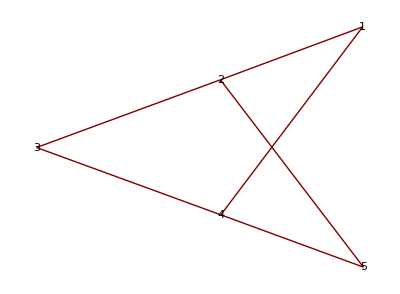

```mathematica
GraphPlot[InfiniteTake[myInfiniteGraph,5,5],VertexLabeling->True]
```

```mathematica
Manipulate[GraphPlot[InfiniteTake[myInfiniteGraph,n,n],DirectedEdges->True,VertexLabeling->True],{n,1,4,1}]
```

```mathematica
Manipulate[GraphPlot[InfiniteTake[InfiniteMatrix[If[Mod[#2,#1]==0&&#1>1,1,0]&],x,x],DirectedEdges->True,VertexLabeling->True],{x,1,2,1}]
```

#### Beginning of working definition: InfiniteMatrixPlus, InfiniteMatrixTimes

```mathematica
InfiniteMatrixPlus[InfiniteMatrix[rule1_],InfiniteMatrix[rule2_]]:= InfiniteMatrix[rule1[#1,#2]+rule2[#1,#2]&]
```

```mathematica
InfiniteMatrixTimes[alpha_Integer,InfiniteMatrix[rule_]]:= InfiniteMatrix[Times[alpha,rule[#1,#2]]&]
```

```mathematica
InfiniteMatrixTimes[alpha_Real,InfiniteMatrix[rule_]]:=        InfiniteMatrix[Times[alpha,rule[#1,#2]]&]
```

```mathematica
(*Because of the infinite sum, Matrix multiplication  is only simbolically defined*)(*OR, we can use a "precision factor" N,   to get until the Nth index in the sum *)
```

```mathematica
InfiniteMatrixTimes[InfiniteMatrix[rule1_],InfiniteMatrix[rule2_]]:=With[
{newrule= Sum[Times[rule1[#1,k],rule2[k,#2]],{k,1,Infinity}]&},
InfiniteMatrix[newrule]]
```

#### End of working definition

#### Scratch

```mathematica
InfiniteMatrixPlus[InfiniteMatrix[#1*#2&],InfiniteMatrix[-#1*#2&]]//InfiniteTake[#,3,4]&
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
InfiniteMatrixTimes[0, InfiniteMatrix[#1+#2&]]//InfiniteTake[#,4,6]&
```

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

```mathematica
InfiniteMatrixTimes[0.2, InfiniteMatrix[#1+#2&]]//InfiniteTake[#,4,6]&
```

{{0.4,0.6,0.8,1.,1.2,1.4},{0.6,0.8,1.,1.2,1.4,1.6},{0.8,1.,1.2,1.4,1.6,1.8},{1.,1.2,1.4,1.6,1.8,2.}}

```mathematica
?Sum
```

Sum[f,{i,i_max}] evaluates the sum ∑_(i=1)^i_max f. 
Sum[f,{i,i_min,i_max}] starts with i=i_min. 
Sum[f,{i,i_min,i_max,di}] uses steps di. 
Sum[f,{i,{i_1,i_2,…}}] uses successive values i_1, i_2, ….
Sum[f,{i,i_min,i_max},{j,j_min,j_max},…] evaluates the multiple sum ∑_(i=i_min)^i_max ∑_(j=j_min)^j_max …f. 
Sum[f,i] gives the indefinite sum ∑_i f.

```mathematica
InfiniteMatrixTimes[InfiniteMatrix[If[#1<3&&#2<7,#1*Pi,0]&],InfiniteMatrix[If[#1<5&&#2<6,#2*E,0]&]]//InfiniteTake[#,8,8]&//MatrixForm
```

(4 ⅇ π | 8 ⅇ π | 12 ⅇ π | 16 ⅇ π | 20 ⅇ π | 0 | 0 | 0
8 ⅇ π | 16 ⅇ π | 24 ⅇ π | 32 ⅇ π | 40 ⅇ π | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

InfiniteMatrixTimes worked well for matrices with finite support (but this finiteness muss be put in the generating rule!)

```mathematica
InfiniteMatrixTimes[InfiniteMatrix[2^{-#1}+0*#2&],InfiniteMatrix[2^{-#2}+0*#1&]]//InfiniteTake[#,8,8]&//MatrixForm
```

Sum::div: Sum does not converge.

General::stop: Further output of Sum::div will be suppressed during this calculation.

((∑_(k=1)^∞ 1/4) | (∑_(k=1)^∞ 1/8) | (∑_(k=1)^∞ 1/16) | (∑_(k=1)^∞ 1/32) | (∑_(k=1)^∞ 1/64) | (∑_(k=1)^∞ 1/128) | (∑_(k=1)^∞ 1/256) | (∑_(k=1)^∞ 1/512)
(∑_(k=1)^∞ 1/8) | (∑_(k=1)^∞ 1/16) | (∑_(k=1)^∞ 1/32) | (∑_(k=1)^∞ 1/64) | (∑_(k=1)^∞ 1/128) | (∑_(k=1)^∞ 1/256) | (∑_(k=1)^∞ 1/512) | (∑_(k=1)^∞ 1/1024)
(∑_(k=1)^∞ 1/16) | (∑_(k=1)^∞ 1/32) | (∑_(k=1)^∞ 1/64) | (∑_(k=1)^∞ 1/128) | (∑_(k=1)^∞ 1/256) | (∑_(k=1)^∞ 1/512) | (∑_(k=1)^∞ 1/1024) | (∑_(k=1)^∞ 1/2048)
(∑_(k=1)^∞ 1/32) | (∑_(k=1)^∞ 1/64) | (∑_(k=1)^∞ 1/128) | (∑_(k=1)^∞ 1/256) | (∑_(k=1)^∞ 1/512) | (∑_(k=1)^∞ 1/1024) | (∑_(k=1)^∞ 1/2048) | (∑_(k=1)^∞ 1/4096)
(∑_(k=1)^∞ 1/64) | (∑_(k=1)^∞ 1/128) | (∑_(k=1)^∞ 1/256) | (∑_(k=1)^∞ 1/512) | (∑_(k=1)^∞ 1/1024) | (∑_(k=1)^∞ 1/2048) | (∑_(k=1)^∞ 1/4096) | (∑_(k=1)^∞ 1/8192)
(∑_(k=1)^∞ 1/128) | (∑_(k=1)^∞ 1/256) | (∑_(k=1)^∞ 1/512) | (∑_(k=1)^∞ 1/1024) | (∑_(k=1)^∞ 1/2048) | (∑_(k=1)^∞ 1/4096) | (∑_(k=1)^∞ 1/8192) | (∑_(k=1)^∞ 1/16384)
(∑_(k=1)^∞ 1/256) | (∑_(k=1)^∞ 1/512) | (∑_(k=1)^∞ 1/1024) | (∑_(k=1)^∞ 1/2048) | (∑_(k=1)^∞ 1/4096) | (∑_(k=1)^∞ 1/8192) | (∑_(k=1)^∞ 1/16384) | (∑_(k=1)^∞ 1/32768)
(∑_(k=1)^∞ 1/512) | (∑_(k=1)^∞ 1/1024) | (∑_(k=1)^∞ 1/2048) | (∑_(k=1)^∞ 1/4096) | (∑_(k=1)^∞ 1/8192) | (∑_(k=1)^∞ 1/16384) | (∑_(k=1)^∞ 1/32768) | (∑_(k=1)^∞ 1/65536))

#### Beginning of working definition: InfinitePolyTimes

```mathematica
(*multiplication of infinite polynomials!*)
```

```mathematica
InfinitePolyTimes[InfiniteList[1,rule1_],InfiniteList[1,rule2_]]:=
With[{newrule=Sum[Times[rule1[j],rule2[#+1-j]],{j,1,#}]&
},InfiniteList[1,newrule]]
```

```mathematica
(*the term #+1-j is there because I have defined infinite lists of direction 1 as starting with index 1*)
```

#### End of working definition

#### Scratch

```mathematica
InfinitePolyTimes[InfiniteList[1, Which[#==1,-1,#==3,1,True,0]&],InfiniteList[1,Which[OddQ[#]&&#≤5,1,True,0]&]]//InfiniteTake[#,10]&
```

{-1,0,0,0,0,0,1,0,0,0}

```mathematica
(*this is the operation:    (x^2 -1)* (x^4 + x^2 + 1) = (x^6 - 1)       *)
```

```mathematica
Table[{i,j},{i,1,10},{j,1,11}]//Take[#,{3,5},{2,6}]&//MatrixForm
```

((3
2) | (3
3) | (3
4) | (3
5) | (3
6)
(4
2) | (4
3) | (4
4) | (4
5) | (4
6)
(5
2) | (5
3) | (5
4) | (5
5) | (5
6))

```mathematica
InfinitePolyTimes[InfiniteList[1, #&],InfiniteList[1,-#^3&]]//InfiniteTake[#,15]&
```

{-1,-10,-46,-146,-371,-812,-1596,-2892,-4917,-7942,-12298,-18382,-26663,-37688,-52088}

#### Beginning of working definition: InfiniteCellularAutomaton

```mathematica
(*this is a cellular automaton that accepts an infinite list as an initial condition, 
it is a direction 1 infinite list, of direction 0 infinite lists.*)
```

```mathematica
ClearAll[InfiniteCellularAutomatonStep];Clear[InfiniteCellularAutomatonStep];Clear[InfiniteCellularAutomaton];
ClearAll[InfiniteCellularAutomaton]
```

```mathematica
InfiniteCellularAutomatonStep[cellularrule_,InfiniteList[0,rule_ ]]:=
With[{newrule=Part[CellularAutomaton[cellularrule,{rule@(#-1),rule@#,rule@(#+1)}],2]&
}, InfiniteList[0,newrule]]
```

```mathematica
InfiniteCellularAutomatonStep[cellularrule_,InfiniteList[0,rule_],n_Integer]:=
NestList[InfiniteCellularAutomatonStep[cellularrule,#]&,InfiniteList[0,rule],n]
```

```mathematica
InfiniteCellularAutomatonStep[cellularrule_,InfiniteList[0,rule_],1]:=InfiniteList[0,rule]
```

```mathematica
InfiniteCellularAutomaton[cellularrule_,InfiniteList[0,rule_]]:=InfiniteList[1,InfiniteCellularAutomatonStep[cellularrule,InfiniteList[0,rule],#]&]
```

```mathematica
InfiniteCellularAutomatonData1[cellularrule_,InfiniteList[0,rule_],{n1_,n2_},t_]:=
Map[InfiniteTake[#,{n1,n2}]&,InfiniteCellularAutomaton[cellularrule,InfiniteList[0,rule]][t]]
```

```mathematica
InfiniteCellularAutomatonData1[cellularrule_,InfiniteList[0,rule_],n_,t_]:=InfiniteCellularAutomatonData1[cellularrule,InfiniteList[0,rule],{-n,n},t]
```

```mathematica
InfiniteCellularAutomatonPlot1[cellularrule_,InfiniteList[0,rule_],{n1_,n2_},t_]:=
ArrayPlot[InfiniteCellularAutomatonData1[cellularrule,InfiniteList[0,rule],{n1,n2},t]]
```

```mathematica
InfiniteCellularAutomatonPlot1[cellularrule_,InfiniteList[0,rule_],n_,t_]:=
ArrayPlot[InfiniteCellularAutomatonData1[cellularrule,InfiniteList[0,rule],n,t]]
```

```mathematica
InfiniteCellularAutomatonData2[cellularrule_,InfiniteList[0,rule_],{n1_,n2_},t_]:=
CellularAutomaton[cellularrule,InfiniteTake[InfiniteList[0,rule],{n1,n2}],t]
```

```mathematica
InfiniteCellularAutomatonData2[cellularrule_,InfiniteList[0,rule_],n_,t_]:=
InfiniteCellularAutomatonData2[cellularrule,InfiniteList[0,rule],{-n,n},t]
```

```mathematica
InfiniteCellularAutomatonPlot2[cellularrule_,InfiniteList[0,rule_],{n1_,n2_},t_]:=
ArrayPlot[InfiniteCellularAutomatonData2[cellularrule,InfiniteList[0,rule],{n1,n2},t]]
```

```mathematica
InfiniteCellularAutomatonPlot2[cellularrule_,InfiniteList[0,rule_],n_,t_]:=
ArrayPlot[InfiniteCellularAutomatonData2[cellularrule,InfiniteList[0,rule],n,t]]
```

#### End of working definition

#### Scratch

```mathematica
Nest[#^2 &,2,5]
```

4294967296

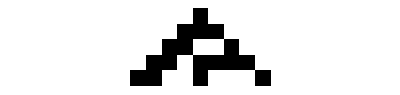

```mathematica
InfiniteCellularAutomaton[30,InfiniteList[0,If[#==0,1,0]&]][4]//Map[InfiniteTake[#,{-10,10}]&,#]&//ArrayPlot
```

```mathematica
InfiniteCellularAutomatonData1[30,InfiniteList[0,If[#==0,1,0]&],10,4]
```

{{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,1,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,1,0,1,1,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,0,0,1,0,0,0,1,0,0,0,0,0,0}}

```mathematica
InfiniteCellularAutomatonPlot1[30,InfiniteList[0,If[#==0,1,0]&],10,4]
```

-Graphics-

```mathematica
InfiniteCellularAutomatonData2[30,InfiniteList[0,If[#==0,1,0]&],10,4]
```

{{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,1,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,1,0,1,1,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,0,0,1,0,0,0,1,0,0,0,0,0,0}}

```mathematica
ArrayPlot[InfiniteCellularAutomatonData2[30,InfiniteList[0,If[#==0,1,0]&],10,4]]
```

-Graphics-

```mathematica
?NestList
```

NestList[f,expr,n] gives a list of the results of applying f to expr 0 through n times.

```mathematica
InfiniteCellularAutomatonStep[30,InfiniteList[0,If[#==0,1,0]&],2]
```

{InfiniteList[0,If[#1==0,1,0]&],InfiniteList[0,CellularAutomaton[30,{(If[#1==0,1,0]&)[#1-1],(If[#1==0,1,0]&)[#1],(If[#1==0,1,0]&)[#1+1]}]⟦2⟧&],InfiniteList[0,CellularAutomaton[30,{(CellularAutomaton[30,{(If[#1==0,1,0]&)[#1-1],(If[#1==0,1,0]&)[#1],(If[#1==0,1,0]&)[#1+1]}]⟦2⟧&)[#1-1],(CellularAutomaton[30,{(If[#1==0,1,0]&)[#1-1],(If[#1==0,1,0]&)[#1],(If[#1==0,1,0]&)[#1+1]}]⟦2⟧&)[#1],(CellularAutomaton[30,{(If[#1==0,1,0]&)[#1-1],(If[#1==0,1,0]&)[#1],(If[#1==0,1,0]&)[#1+1]}]⟦2⟧&)[#1+1]}]⟦2⟧&]}

```mathematica
NestList[InfiniteCellularAutomatonStep[30,#]&,InfiniteList[0,If[#==0,1,0]&],2]
```

{InfiniteList[0,If[#1==0,1,0]&],InfiniteList[0,CellularAutomaton[30,{(If[#1==0,1,0]&)[#1-1],(If[#1==0,1,0]&)[#1],(If[#1==0,1,0]&)[#1+1]}]⟦2⟧&],InfiniteList[0,CellularAutomaton[30,{(CellularAutomaton[30,{(If[#1==0,1,0]&)[#1-1],(If[#1==0,1,0]&)[#1],(If[#1==0,1,0]&)[#1+1]}]⟦2⟧&)[#1-1],(CellularAutomaton[30,{(If[#1==0,1,0]&)[#1-1],(If[#1==0,1,0]&)[#1],(If[#1==0,1,0]&)[#1+1]}]⟦2⟧&)[#1],(CellularAutomaton[30,{(If[#1==0,1,0]&)[#1-1],(If[#1==0,1,0]&)[#1],(If[#1==0,1,0]&)[#1+1]}]⟦2⟧&)[#1+1]}]⟦2⟧&]}

#### Scratch

```mathematica
myInitialCondition=InfiniteList[0,If[#==0,1,0]&]
```

InfiniteList[0,If[#1==0,1,0]&]

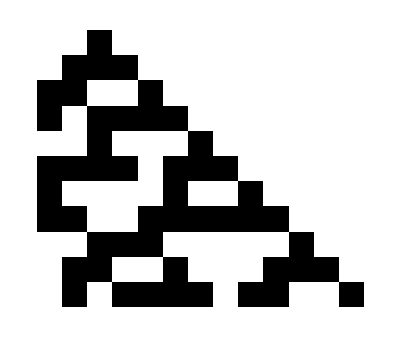

```mathematica
InfiniteCellularAutomatonPlot1[30,myInitialCondition,{-2,10},10]
```

```mathematica
InfiniteCellularAutomatonPlot2[30,myInitialCondition,{-5,25},20]
```

-Graphics-

```mathematica
TuringMachine[2506,{1,{{},0}},10]//Grid
```

{1,3,0} | {0,0,0,0,0,0}
{2,4,1} | {0,0,1,0,0,0}
{1,3,0} | {0,0,1,1,0,0}
{2,2,-1} | {0,0,0,1,0,0}
{1,1,-2} | {0,1,0,1,0,0}
{2,2,-1} | {1,1,0,1,0,0}
{1,3,0} | {1,0,0,1,0,0}
{2,4,1} | {1,0,1,1,0,0}
{1,5,2} | {1,0,1,0,0,0}
{2,6,3} | {1,0,1,0,1,0}
{1,5,2} | {1,0,1,0,1,1}

```mathematica
?TuringMachine
```

TuringMachine[rule,init,t] generates a list representing the evolution of the Turing machine with the specified rule from initial condition init for t steps. 
TuringMachine[rule,init] gives the result of evolving init for one step. 
TuringMachine[rule] is an operator form of TuringMachine that corresponds to one step of evolution.

```mathematica
Range[10][[{1,5}]]
```

{1,5}

#### Beginning of working definition: InfiniteTuring

```mathematica
(*InfiniteTuringState:={{state,displacement}, InfiniteList[0,rule]}*)
```

```mathematica
Clear[NextInfiniteTuringState]
```

```mathematica
Clear[AuxiliarTuringFunction]
```

```mathematica
AuxiliarTuringFunction[turingrule_,{{state_,2},{x_,y_,z_}}]:=
TuringMachine[turingrule,{{state,2},{x,y,z}}] (*the idea of this function is to calculate locally for the next step*)
```

```mathematica
NextInfiniteTuringState[turingrule_,{{state_,displacement_}, InfiniteList[0,rule_]}]:=
Module[
{newrule,auxvar}, newrule= If[#<displacement-1||#>displacement+1,rule@#,
TuringMachine[turingrule,{{state,#-displacement+2},  {rule@(#-1),rule@#,rule@(#+1)}} ][[2]] [[#-displacement+2]] 
]&;
	auxvar=TuringMachine[turingrule,{{state,1},  {rule@(displacement-1),rule@displacement,rule@(displacement+1)}}][[1]];

{{auxvar[[1]],displacement+auxvar[[3]]},InfiniteList[0,newrule]}]
```

```mathematica
NextInfiniteTuringState2[turingrule_,{{state_,displacement_},InfiniteList[0,rule_]}]:=
Module[
{newrule,auxvar},
auxvar= AuxiliarTuringFunction[turingrule,{{state,2},
{rule@(displacement-1),rule@displacement,rule@(displacement+1)}}];
newrule=If[(#<displacement-1||#>displacement+1),rule@#,auxvar[[2]]][[#-displacement+2]]&;
{{auxvar[[1]][[1]],auxvar[[1]][[3]]+displacement},InfiniteList[0,newrule]}
]
```

```mathematica
Clear[InfiniteTuringMachine]
```

```mathematica
InfiniteTuringMachine[turingrule_,{{initialstate_,initialdisplacement_:0},InfiniteList[0,rule_]},steps_]:=
NestList[ NextInfiniteTuringState[turingrule,#]&
,{{initialstate,initialdisplacement},InfiniteList[0,rule]},steps]
```

```mathematica
InfiniteTuringMachine2[turingrule_,{{initialstate_,initialdisplacement_:0},InfiniteList[0,rule_]},steps_]:=
NestList[ NextInfiniteTuringState2[turingrule,#]&
,{{initialstate,initialdisplacement},InfiniteList[0,rule]},steps]
```

#### End of working definition

#### Scratch

```mathematica
AuxiliarTuringFunction[2506,{{2,2},{1,0,0}}]
```

{{1,1,-1},{1,1,0}}

```mathematica
NextInfiniteTuringState[2506,{{1,0},InfiniteList[0,x↦0]}]
```

{{2,1},InfiniteList[0,If[#1<0-1||#1>0+1,Function[x,0][#1],TuringMachine[2506,{{1,#1-0+2},{Function[x,0][#1-1],Function[x,0][#1],Function[x,0][#1+1]}}]⟦2⟧⟦#1-0+2⟧]&]}

```mathematica
InfiniteTake[NextInfiniteTuringState[{2139050,3},{{1,0},InfiniteList[0,x↦Mod[x,2]]}][[2]],{-5,5}]
```

{1,0,1,0,1,1,1,0,1,0,1}

```mathematica
InfiniteTuringMachine2[2506,{{1,0},InfiniteList[0,x↦0]},2]//Column
```

Part::partd: Part specification 0⟦4⟧ is longer than depth of object.

{{1,0},InfiniteList[0,Function[x,0]]}
{{2,1},InfiniteList[0,If[#1<0-1||#1>0+1,Function[x,0][#1],auxvar$15552⟦2⟧]⟦#1-0+2⟧&]}
{{1,0},InfiniteList[0,If[#1<1-1||#1>1+1,(If[#1<0-1||#1>0+1,Function[x,0][#1],auxvar$15552⟦2⟧]⟦#1-0+2⟧&)[#1],auxvar$15560⟦2⟧]⟦#1-1+2⟧&]}

```mathematica
Map[InfiniteTake[#[[2]],{-5,5}]&,InfiniteTuringMachine2[2506,{{1,0},InfiniteList[0,x↦0]},2]]//Column
```

Part::partd: Part specification 0⟦4⟧ is longer than depth of object.

Part::partd: Part specification 0⟦-3⟧ is longer than depth of object.

Part::partd: Part specification 0⟦-2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part -4 of 0⟦-3⟧ does not exist.

Part::partw: Part -3 of 0⟦-2⟧ does not exist.

Part::partw: Part 4 of 0⟦5⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{0,0,0,0,0,0,0,0,0,0,0}
{0⟦-3⟧,0⟦-2⟧,0⟦-1⟧,Integer,0,1,0,0⟦4⟧,0⟦5⟧,0⟦6⟧,0⟦7⟧}
{0⟦-3⟧⟦-4⟧,0⟦-2⟧⟦-3⟧,0,Integer⟦-1⟧,Integer,1,1,0⟦4⟧,0⟦5⟧⟦4⟧,0⟦6⟧⟦5⟧,0⟦7⟧⟦6⟧}